```mathematica
Λ = 1
ϕcosmological = .001
ρ = 10
Subscript[R, c]= 1
```

1

0.001

10

1

```mathematica
startI = .1
endI = 1
```

0.1

1

```mathematica
backgroundsolutioninterior = NDSolve[{1/Subscript[R, c]^2 D[ϕ[r],r,r]+2/(r Subscript[R, c])D[ϕ[r],r]+2/Λ^2(4/(r Subscript[R, c])D[ϕ[r],r]+ 2/(r^2 Subscript[R, c]^2)(D[ϕ[r],r])^2)==8π ρ,ϕ'[startI] == 0,ϕ[endI] ==  ϕcosmological},
ϕ,{r,startI,endI}]
```

{{ϕ→InterpolatingFunction[{{0.1, 1.}}, <>]}}

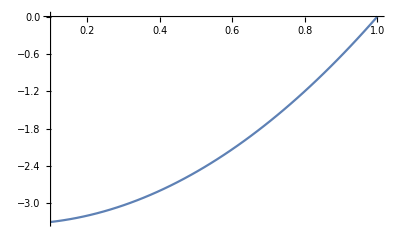

```mathematica
Plot[ϕ[r]/.backgroundsolutioninterior,{r,startI,endI}]
```

```mathematica
startE = 1
endE = 100
```

1

100

```mathematica
backgroundsolutionexterior = NDSolve[{1/Subscript[R, c]^2 D[ϕ[r],r,r]+2/(r Subscript[R, c])D[ϕ[r],r]+2/Λ^2(4/(r Subscript[R, c])D[ϕ[r],r]+ 2/(r^2 Subscript[R, c]^2)(D[ϕ[r],r])^2)==0,ϕ[startE] ==  ϕcosmological*1.1,ϕ[endE] ==  ϕcosmological},
ϕ,{r,startE,endE}]
```

{{ϕ→InterpolatingFunction[{{1., 100.}}, <>]}}

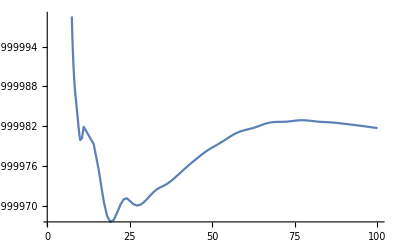

```mathematica
Plot[ϕ[r]/.backgroundsolutionexterior,{r,startE,endE}]
```